## Preload

#### Once

imp = Import[FileNameJoin[{$here, "download", "test.csv"}], "CSV", "HeaderLines" -> 1];
Export[
 FileNameJoin[{$here, "download", "test.wxf"}],
 BinarySerialize[Image@Partition[#, 28] & /@ imp]
 ]

#### Load

```mathematica
CC;$here=NotebookDirectory[];$now=Now
Get[$here<>"test.m",CharacterEncoding->"UTF8"];
$test=BinaryDeserialize@Import[
FileNameJoin[{$here,"download","test.wxf"}]
];
```

所有临时定义已清空!

Sat 21 Apr 2018 14:19:37GMT+8.

## LeNet

#### Load Net

NetChain[<>]

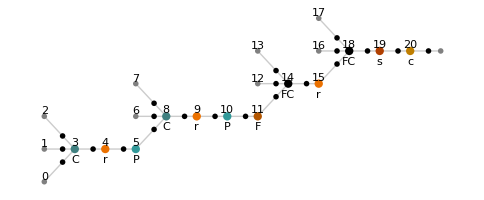

```mathematica
LeNetInit=NetInitialize@NetChain[{
ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],
ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],
FlattenLayer[],500,Ramp,10,SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",Range[0,9]}],
"Input"->NetEncoder[{"Image",{28,28},"Grayscale"}]
];
LeNet=NetModel["LeNet Trained on MNIST Data"]
info=Magnify[NetInformation[LeNet,"MXNetNodeGraphPlot"],2]
```

#### Export

```mathematica
Exporter@LeNet[$test];//TT
```

CPU Time:  3.40625

All Time:  13.5783

## CapsNet

#### Load Net

NetGraph[<>]

-Graphics-

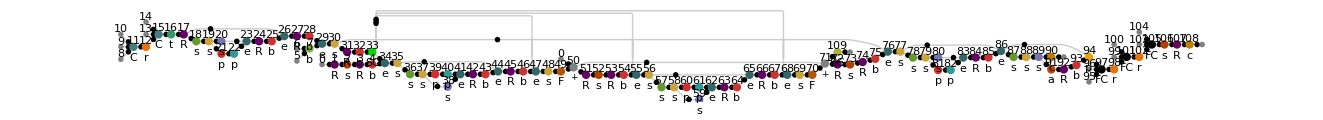

```mathematica
CapsNet=NetModel["CapsNet Trained on MNIST Data"]
info=Magnify[NetInformation[CapsNet,"FullSummaryGraphic"],2]
ni=NetInformation[CapsNet,"MXNetNodeGraphPlot"];
fLL[list_]:=Multicolumn[Map[Row @ {First@#, " ", Last@#}&,list], {Automatic, 12}]
Magnify[Legended[ni//First,Placed[ni[[-1,1]]/.(LegendLayout ->a_)->(LegendLayout ->fLL),Below]],2]
```

#### Export

```mathematica
Exporter[CapsNet[$test]["Classification"]];//TT
```

CPU Time:  9.09375

All Time:  1968.5